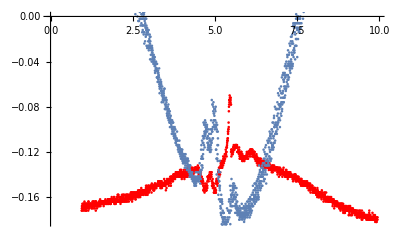

```mathematica
SetDirectory[NotebookDirectory[]];
las=Drop[Drop[Import["../osc/ALL0002/F0002CH1.CSV", {"Data", All, {4,5}}], -13],237];
pd = Drop[Drop[Import["../osc/ALL0002/F0002CH2.CSV",{"Data",All,{4,5}}],237], -13];
Show[ListPlot[Map[{#[[1]],#[[2]]*5-0.0388*5}&,pd],PlotStyle->Red],ListPlot[Map[{#[[1]],#[[2]]-1.17 }&,las]]]
```

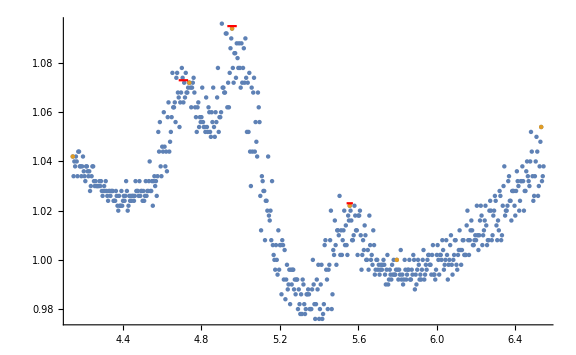

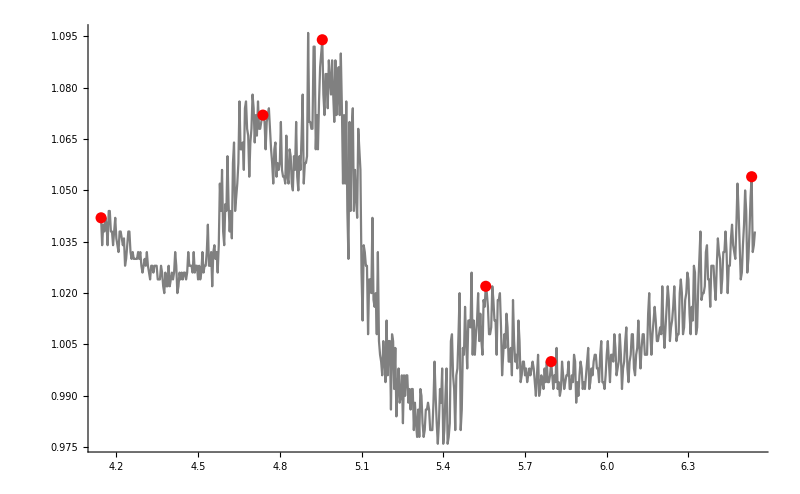

{4.738,4.956,5.556}

```mathematica
las=Drop[Drop[Import["../osc/ALL0002/F0002CH1.CSV", {"Data", All, {4,5}}], -13],237];
t = TimeSeries[las[[800;;1400]]];
Show[ListPlot[{t,FindPeaks[t,5.5]}],Plot[1.073,{x,4.708-0.024, 4.708+0.024},PlotStyle->Red],Plot[1.095,{x, 4.956-0.024,4.956+0.024},PlotStyle->Red],Plot[1.023,{x, 5.556-0.016,5.556+0.016},PlotStyle->Red],ImageSize->Large]
Show[{ListLinePlot[t,PlotStyle->Gray],ListPlot[FindPeaks[t,5.5],PlotStyle->{Red,PointSize->0.01}]},ImageSize->800]
FindPeaks[t,5.5]["PathTimes"][[2;;4]]
```

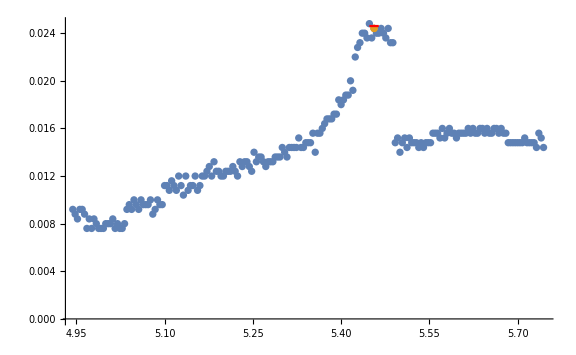

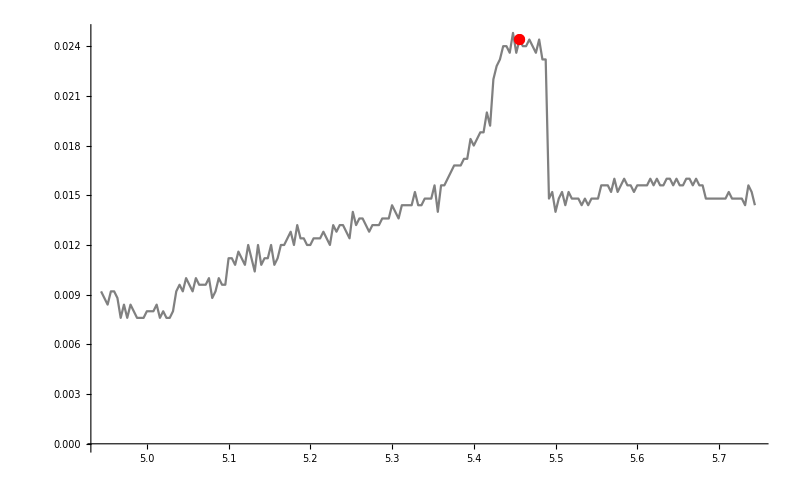

{5.456}

```mathematica
pd = Drop[Drop[Import["../osc/ALL0002/F0002CH2.CSV",{"Data",All,{4,5}}],237], -13];
ts = TimeSeries[pd[[1000;;1200]]];
Show[ListPlot[{ts,FindPeaks[ts,100]}],Plot[0.0246,{x,5.456-0.008,5.456+0.008},PlotStyle->Red],ImageSize->Large]
Show[{ListLinePlot[ts,PlotStyle->Gray],ListPlot[FindPeaks[ts,100],PlotStyle->{Red,PointSize->0.01}]},ImageSize->800]
FindPeaks[ts,100]["PathTimes"]
```